# Chapter 3 Experimental Errors and Error Analysis

This chapter is largely a tutorial on handling experimental errors of measurement. Much of the material has been extensively tested with science undergraduates at a variety of levels at the University of Toronto.

Whole books can and have been written on this topic but here we distill the topic down to the essentials. Nonetheless, our experience is that for beginners an iterative approach to this material works best. This means that the users first scan the material in this chapter; then try to use the material on their own experiment; then go over the material again; then ...

EDA provides functions to ease the calculations required by propagation of errors, and those functions are introduced in Section 3.3. These error propagation functions are summarized in Section 3.5.

## 3.1 Introduction

### 3.1.1 The Purpose of Error Analysis

For students who only attend lectures and read textbooks in the sciences, it is easy to get the incorrect impression that the physical sciences are concerned with manipulating precise and perfect numbers. Lectures and textbooks often contain phrases like:

A particle falling under the influence of gravity is subject to a constant acceleration of 9.8 m/s^2. If ...

For an experimental scientist this specification is incomplete. Does it mean that the acceleration is closer to 9.8 than to 9.9 or 9.7?  Does it mean that the acceleration is closer to 9.80000 than to 9.80001 or 9.79999?  Often the answer depends on the context. If a carpenter says a length is “just 8 inches” that probably means the length is closer to 8 0/16 in. than to 8 1/16 in. or 7 15/16 in. If a machinist says a length is “just 200 millimeters” that probably means it is closer to 200.00 mm than to 200.05 mm or 199.95 mm.

We all know that the acceleration due to gravity varies from place to place on the earth’s surface. It also varies with the height above the surface, and gravity meters capable of measuring the variation from the floor to a tabletop are readily available. Further, any physical measure such as g can only be determined by means of an experiment, and since a perfect experimental apparatus does not exist, it is impossible even in principle to ever know g perfectly. Thus, the specification of g given above is useful only as a possible exercise for a student. In order to give it some meaning it must be changed to something like:

A 5 g ball bearing falling under the influence of gravity in Room 126 of McLennan Physical Laboratories of the University of Toronto on March 13, 1995 at a distance of 1.0 ± 0.1 m above the floor was measured to be subject to a constant acceleration of 9.81 ± 0.03 m/s^2.

Two questions arise about the measurement. First, is it “accurate,” in other words, did the experiment work properly and were all the necessary factors taken into account?  The answer to this depends on the skill of the experimenter in identifying and eliminating all systematic errors. These are discussed in Section 3.4.

The second question regards the “precision” of the experiment. In this case the precision of the result is given: the experimenter claims the precision of the result is within 0.03 m/s^2. The next two sections go into some detail about how the precision of a measurement is determined. However, the following points are important:

1. The person who did the measurement probably had some “gut feeling” for the precision and “hung” an error on the result primarily to communicate this feeling to other people. Common sense should always take precedence over mathematical manipulations.

2. In complicated experiments, error analysis can identify dominant errors and hence provide a guide as to where more effort is needed to improve an experiment.

3. There is virtually no case in the experimental physical sciences where the correct error analysis is to compare the result with a number in some book. A correct experiment is one that is performed correctly, not one that gives a result in agreement with other measurements.

4. The best precision possible for a given experiment is always limited by the apparatus. Polarization measurements in high-energy physics require tens of thousands of person-hours and cost hundreds of thousand of dollars to perform, and a good measurement is within a factor of two. Electrodynamics experiments are considerably cheaper, and often give results to 8 or more significant figures. In both cases, the experimenter must struggle with the equipment to get the most precise and accurate measurement possible.

### 3.1.2 Different Types of Errors

As mentioned above, there are two types of errors associated with an experimental result: the “precision” and the “accuracy”. One well-known text explains the difference this way:

The word “precision” will be related to the random error distribution associated with a particular experiment or even with a particular type of experiment. The word “accuracy” shall be related to the existence of systematic errors—differences between laboratories, for instance. For example, one could perform very precise but inaccurate timing with a high-quality pendulum clock that had the pendulum set at not quite the right length. E.M. Pugh and G.H. Winslow, p. 6.

The object of a good experiment is to minimize both the errors of precision and the errors of accuracy.

Usually, a given experiment has one or the other type of error dominant, and the experimenter devotes the most effort toward reducing that one. For example, in measuring the height of a sample of geraniums to determine an average value, the random variations within the sample of plants are probably going to be much larger than any possible inaccuracy in the ruler being used. Similarly for many experiments in the biological and life sciences, the experimenter worries most about increasing the precision of his/her measurements. Of course, some experiments in the biological and life sciences are dominated by errors of accuracy.

On the other hand, in titrating a sample of HCl acid with NaOH base using a phenolphthalein indicator, the major error in the determination of the original concentration of the acid is likely to be one of the following: (1) the accuracy of the markings on the side of the burette; (2) the transition range of the phenolphthalein indicator; or (3) the skill of the experimenter in splitting the last drop of NaOH. Thus, the accuracy of the determination is likely to be much worse than the precision. This is often the case for experiments in chemistry, but certainly not all.

Question: Most experiments use theoretical formulas, and usually those formulas are approximations. Is the error of approximation one of precision or of accuracy?

### 3.1.3 References

There is extensive literature on the topics in this chapter. The following lists some well-known introductions.

D.C. Baird, Experimentation: An Introduction to Measurement Theory and Experiment Design (Prentice-Hall, 1962)

E.M. Pugh and G.H. Winslow, The Analysis of Physical Measurements (Addison-Wesley, 1966)

J.R. Taylor, An Introduction to Error Analysis (University Science Books, 1982)

In addition, there is a web document written by the author of EDA that is used to teach this topic to first year Physics undergraduates at the University of Toronto. The following Hyperlink points to that document.

http://www.upscale.utoronto.ca/PVB/Harrison/ErrorAnalysis/

## 3.2 Determining the Precision

### 3.2.1 The Standard Deviation

In the nineteenth century, Gauss’ assistants were doing astronomical measurements. However, they were never able to exactly repeat their results. Finally, Gauss got angry and stormed into the lab, claiming he would show these people how to do the measurements once and for all. The only problem was that Gauss wasn’t able to repeat his measurements exactly either!

After he recovered his composure, Gauss made a histogram of the results of a particular measurement and discovered the famous Gaussian or bell-shaped curve.

Many people’s first introduction to this shape is the grade distribution for a course. Here is a sample of such a distribution, using the Histogram function which is built-in in Mathematica. We will use bin widths of 10.

```mathematica
finalgrades={80,92,72,84,73,76,83,73,77,71,81,67,83,73,62,80,72,78,81,66,64,78,78,64,79,92,76,80,81,85,71,63,74,80,88,70,79,63,93,72,92,75,76,87,74,78,72,89,62,74,2,5,32,27,52,55,58,64,69};
```

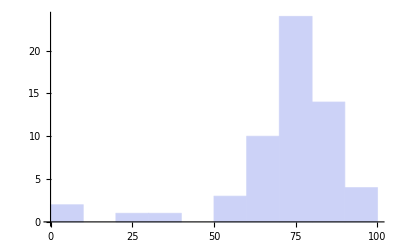

```mathematica
gradeHist=Histogram[finalgrades, 10]
```

We use a standard Mathematica routine to generate a Probability Distribution Function (PDF) of such a “Gaussian” or “normal” distribution. The mean is chosen to be 78 and the standard deviation is chosen to be 10; both the mean and standard deviation are defined below.

```mathematica
dist=PDF[NormalDistribution[78,10],x]
```

(ⅇ^(-1/200 (-78+x)^2))/(10 √(2 π))

We then normalize the distribution so the maximum value is close to the maximum number in the histogram and plot the result.

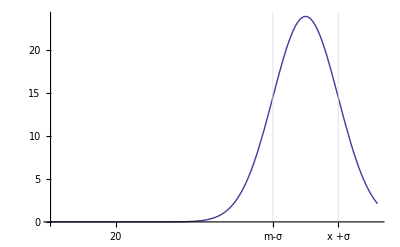

```mathematica
gaussPlot=Plot[(24 dist)/0.04,{x,0,100},Ticks->{{20,40,{78-10,"m-σ"},{78,"x"},{78+10,"x +σ"},100},Automatic},GridLines->{{78-10,78+10},None}]
```

In this graph, x̄ is the mean and σ is the standard deviation.

Finally, we look at the histogram and plot together.

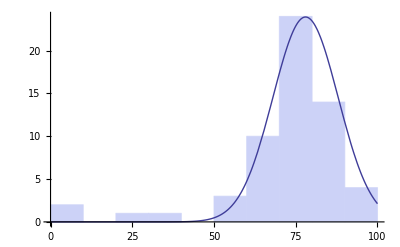

```mathematica
Show[{gradeHist,gaussPlot}]
```

We can see the functional form of the Gaussian distribution by giving NormalDistribution symbolic values.

```mathematica
PDF[NormalDistribution[x̄,σ],x]
```

(ⅇ^(-(x-x̄)^2/(2 σ^2)))/(√(2 π) σ)

In this formula, the quantity x̄ is called the mean, and σ is called the standard deviation. The mean is sometimes called the average. The definition of σ is as follows.

σ≡√Limit[(∑_(i=1)^n (x⟦i⟧- x̄)^2)/n,n→∞]

Here n is the total number of measurements and x[[i]] is the result of measurement number i.

The standard deviation is a measure of the width of the peak, meaning that a larger value gives a wider peak.

If we look at the area under the curve from  x̄ - σ to x̄ + σ, the area between the vertical bars in the gaussPlot graph, we find that this area is 68 percent of the total area. Thus, any result x[[i]] chosen at random has a 68% change of being within one standard deviation of the mean.  We can show this by evaluating the integral.  For convenience, we choose the mean to be zero.

```mathematica
∫_-σ^σ PDF[NormalDistribution[0,σ],x]ⅆx
```

Erf[1/(√2)]

Now, we numericalize this and multiply by 100 to find the percent.

```mathematica
N[%] 100
```

68.2689

The only problem with the above is that the measurement must be repeated an infinite number of times before the standard deviation can be determined. If n is less than infinity, one can only estimate σ. For n measurements, this is the best estimate.

σ_est =√((∑_(i=1)^n (x⟦i⟧- x̄)^2)/(n-1))

The major difference between this estimate and the definition is the (n - 1) in the denominator instead of n. This is reasonable since if n = 1 we know we can’t determine σ at all since with only one measurement we have no way of determining how closely a repeated measurement might give the same result. Technically, the quantity (n - 1) is the “number of degrees of freedom” of the sample of measurements.

Here is an example. Suppose we are to determine the diameter of a small cylinder using a micrometer. We repeat the measurement 10 times along various points on the cylinder and get the following results, in centimeters.

```mathematica
diameter={1.6515,1.6542,1.6500,1.6510,1.6503,1.6540,1.6528,1.6490,1.6520,1.6492};
```

The number of measurements is the length of the list.

```mathematica
n=Length[diameter]
```

10

The average or mean is now calculated.

```mathematica
average=(Plus@@diameter)/Length[diameter]
```

1.6514

Then the standard deviation is estimated to be 0.00185173.

```mathematica
Subscript[σ, est] =Module[
			{sum,i},
			sum=0;
			For[i=1,i≤n,i++,
				sum+=(diameter⟦i⟧-average)^2/(n-1)];
		√sum
]
```

0.00185173

We repeat the calculation in a functional style.

```mathematica
Subscript[σ, est] =√(Plus@@((diameter-average)^2/(n-1)))
```

0.00185173

Note that Mathematica includes functions to calculate all of these quantities and a great deal more.

We close with two points:

1. The standard deviation has been associated with the error in each individual measurement. Section 3.3.2 discusses how to find the error in the estimate of the average.

2. This calculation of the standard deviation is only an estimate. In fact, we can find the expected error in the estimate, Δσ_est, (the error in the estimate!).

```mathematica
Subscript[Δσ, est] =N[Subscript[σ, est]/(√(2 n-2))]
```

0.000436456

As discussed in more detail in Section 3.3, this means that the true standard deviation probably lies in the range of values.

```mathematica
{Subscript[σ, est] - Subscript[Δσ, est], Subscript[σ, est] + Subscript[Δσ, est]}
```

{0.00141527,0.00228818}

Viewed in this way, it is clear that the last few digits in the numbers above for σ_est or Δσ_est have no meaning, and thus are not really significant. An EDA function adjusts these significant figures based on the error.

```mathematica
Needs["EDA`"]
```

```mathematica
AdjustSignificantFigures[{Subscript[σ, est], Subscript[Δσ, est]}]
```

{0.00185,0.00044}

AdjustSignificantFigures is discussed further in Section 3.3.1.

### 3.2.2 The Reading Error

There is another type of error associated with a directly measured quantity, called the “reading error”. Referring again to the example of Section 3.2.1, the measurements of the diameter were performed with a micrometer. The particular micrometer used had scale divisions every 0.001 cm. However, it was possible to estimate the reading of the micrometer between the divisions, and this was done in this example. But, there is a reading error associated with this estimation. For example, the first data point is 1.6515 cm. Could it have been 1.6516 cm instead?  How about 1.6519 cm?  There is no fixed rule to answer the question: the person doing the measurement must guess how well he or she can read the instrument. A reasonable guess of the reading error of this micrometer might be 0.0002 cm on a good day. If the experimenter were up late the night before, the reading error might be 0.0005 cm.

An important and sometimes difficult question is whether the reading error of an instrument is “distributed randomly”.  Random reading errors are caused by the finite precision of the experiment. If an experimenter consistently reads the micrometer 1 cm lower than the actual value, then the reading error is not random.

For a digital instrument, the reading error is ± one-half of the last digit. Note that this assumes that the instrument has been properly engineered to round a reading correctly on the display.

### 3.2.3 “THE” Error

So far, we have found two different errors associated with a directly measured quantity: the standard deviation and the reading error. So, which one is the actual real error of precision in the quantity?  The answer is both!  However, fortunately it almost always turns out that one will be larger than the other, so the smaller of the two can be ignored.

In the diameter example being used in this section, the estimate of the standard deviation was found to be 0.00185 cm, while the reading error was only 0.0002 cm. Thus, we can use the standard deviation estimate to characterize the error in each measurement. Another way of saying the same thing is that the observed spread of values in this example is not accounted for by the reading error. If the observed spread were more or less accounted for by the reading error, it would not be necessary to estimate the standard deviation, since the reading error would be the error in each measurement.

Of course, everything in this section is related to the precision of the experiment. Discussion of the accuracy of the experiment is in Section 3.4.

### 3.2.4 Rejection of Measurements

Often when repeating measurements one value appears to be spurious and we would like to throw it out. Also, when taking a series of measurements, sometimes one value appears “out of line”. Here we discuss some guidelines on rejection of measurements; further information appears in Chapter 7.

It is important to emphasize that the whole topic of rejection of measurements is awkward. Some scientists feel that the rejection of data is never justified unless there is external evidence that the data in question is incorrect. Other scientists attempt to deal with this topic by using quasi-objective rules such as Chauvenet’s Criterion. Still others, often incorrectly, throw out any data that appear to be incorrect. In this section, some principles and guidelines are presented; further information may be found in many references.

First, we note that it is incorrect to expect each and every measurement to overlap within errors. For example, if the error in a particular quantity is characterized by the standard deviation, we only expect 68% of the measurements from a normally distributed population to be within one standard deviation of the mean. Ninety-five percent of the measurements will be within two standard deviations, 99% within three standard deviations, etc., but we never expect 100% of the measurements to overlap within any finite-sized error for a truly Gaussian distribution.

Of course, for most experiments the assumption of a Gaussian distribution is only an approximation.

If the error in each measurement is taken to be the reading error, again we only expect most, not all, of the measurements to overlap within errors. In this case the meaning of “most”, however, is vague and depends on the optimism/conservatism of the experimenter who assigned the error.

Thus, it is always dangerous to throw out a measurement. Maybe we are unlucky enough to make a valid measurement that lies ten standard deviations from the population mean. A valid measurement from the tails of the underlying distribution should not be thrown out. It is even more dangerous to throw out a suspect point indicative of an underlying physical process. Very little science would be known today if the experimenter always threw out measurements that didn’t match preconceived expectations!

In general, there are two different types of experimental data taken in a laboratory and the question of rejecting measurements is handled in slightly different ways for each. The two types of data are the following:

1. A series of measurements taken with one or more variables changed for each data point. An example is the calibration of a thermocouple, in which the output voltage is measured when the thermocouple is at a number of different temperatures.

2. Repeated measurements of the same physical quantity, with all variables held as constant as experimentally possible. An example is the measurement of the height of a sample of geraniums grown under identical conditions from the same batch of seed stock.

For a series of measurements (case 1), when one of the data points is out of line the natural tendency is to throw it out. But, as already mentioned, this means you are assuming the result you are attempting to measure. As a rule of thumb, unless there is a physical explanation of why the suspect value is spurious and it is no more than three standard deviations away from the expected value, it should probably be kept. Chapter 7 deals further with this case.

For repeated measurements (case 2), the situation is a little different. Say you are measuring the time for a pendulum to undergo 20 oscillations and you repeat the measurement five times. Assume that four of these trials are within 0.1 seconds of each other, but the fifth trial differs from these by 1.4 seconds (i.e., more than three standard deviations away from the mean of the “good” values). There is no known reason why that one measurement differs from all the others. Nonetheless, you may be justified in throwing it out. Say that, unknown to you, just as that measurement was being taken, a gravity wave swept through your region of spacetime. However, if you are trying to measure the period of the pendulum when there are no gravity waves affecting the measurement, then throwing out that one result is reasonable. (Although trying to repeat the measurement to find the existence of gravity waves will certainly be more fun!)  So whatever the reason for a suspect value, the rule of thumb is that it may be thrown out provided that fact is well documented and that the measurement is repeated a number of times more to convince the experimenter that he/she is not throwing out an important piece of data indicating a new physical process.

## 3.3 Propagation of Errors of Precision

### 3.3.1 Discussion and Examples

Usually, errors of precision are probabilistic. This means that the experimenter is saying that the actual value of some parameter is probably within a specified range. For example, if the half-width of the range equals one standard deviation, then the probability is about 68% that over repeated experimentation the true mean will fall within the range; if the half-width of the range is twice the standard deviation, the probability is 95%, etc.

If we have two variables, say x and y, and want to combine them to form a new variable, we want the error in the combination to preserve this probability.

The correct procedure to do this is to combine errors in quadrature, which is the square root of the sum of the squares. EDA supplies a Quadrature function.

```mathematica
Needs["EDA`"]
```

```mathematica
Quadrature[a,b,c]
```

√(a^2+b^2+c^2)

```mathematica
Quadrature[3,4]
```

5.

```mathematica
Quadrature[{3,4}]
```

5.

For simple combinations of data with random errors, the correct procedure can be summarized in three rules. Δx, Δy, Δz will stand for the errors of precision in x, y, and z, respectively. We assume that x and y are independent of each other.

Note that all three rules assume that the error, say Δx, is small compared to the value of x.

Rule 1: Multiplication and Division

If

z = x * y

or

z=x/y

then

Δz/z== Quadrature[Δx/x,Δy/x]

In words, the fractional error in z is the quadrature of the fractional errors in x and y.

Rule 2: Addition and Subtraction

If

z = x + y

or

z = x - y

then

Δz == Quadrature[Δx, Δy]

In words, the error in z is the quadrature of the errors in x and y.

Rule 3: Raising to a Power

If

z = x^n

then

Δz == n x^(n - 1) Δx

or equivalently

Δz/z == n Δx/x

EDA includes functions to combine data using the above rules. They are named TimesWithError, PlusWithError, DivideWithError, SubtractWithError, and PowerWithError.

Imagine we have pressure data, measured in centimeters of Hg, and volume data measured in arbitrary units. Each data point consists of {value, error} pairs.

```mathematica
p={{70,0.04},{72,0.04},{74,0.04},{76,0.04},{78,0.04},{80,0.04},{82,0.04},{84,0.04},{86,0.04},{88,0.04},{90,0.04}};
```

```mathematica
v={{11.28156820762763,0.031},{10.98366389613071,0.031},{10.6916855829648,0.031},{10.4292141352925,0.031},{10.15135483487289,0.031},{9.9030178446771,0.031},{9.69180367127115,0.031},{9.45284578420525,0.031},{9.23770984228389,0.031},{9.03759086299312,0.031},{8.84919072382683,0.031}};
```

We calculate the pressure times the volume.

```mathematica
pv=TimesWithError[p,v]
```

{{789.7,2.2},{790.8,2.3},{791.2,2.3},{792.6,2.4},{791.8,2.5},{792.2,2.5},{794.7,2.6},{794.,2.6},{794.4,2.7},{795.3,2.8},{796.4,2.8}}

In the above, the values of p and v have been multiplied and the errors have ben combined using Rule 1.

There is an equivalent form for this calculation.

```mathematica
pv=p ~TimesWithError~ v
```

{{789.7,2.2},{790.8,2.3},{791.2,2.3},{792.6,2.4},{791.8,2.5},{792.2,2.5},{794.7,2.6},{794.,2.6},{794.4,2.7},{795.3,2.8},{796.4,2.8}}

Consider the first of the volume data: {11.28156820762763, 0.031}. The error means that the true value is claimed by the experimenter to probably lie between 11.25 and 11.31. Thus, all the significant figures presented to the right of 11.28 for that data point really aren’t significant. The function AdjustSignificantFigures will adjust the volume data.

```mathematica
AdjustSignificantFigures[v]
```

{{11.282,0.031},{10.984,0.031},{10.692,0.031},{10.429,0.031},{10.151,0.031},{9.903,0.031},{9.692,0.031},{9.453,0.031},{9.238,0.031},{9.038,0.031},{8.849,0.031}}

Notice that by default, AdjustSignificantFigures uses the two most significant digits in the error for adjusting the values. This can be controlled with the ErrorDigits option.

```mathematica
AdjustSignificantFigures[v,ErrorDigits->1]
```

{{11.28,0.03},{10.98,0.03},{10.69,0.03},{10.43,0.03},{10.15,0.03},{9.9,0.03},{9.69,0.03},{9.45,0.03},{9.24,0.03},{9.04,0.03},{8.85,0.03}}

For most cases, the default of two digits is reasonable. As discussed in Section 3.2.1, if we assume a normal distribution for the data, then the fractional error in the determination of the standard deviation σ depends on the number of data points used in its calculation, n, and can be written as follows.

Δσ/σ=1/(√(2 n-2))

Thus, using this as a general rule of thumb for all errors of precision, the estimate of the error is only good to 10%, (i.e. one significant figure, unless n is greater than 51) . Nonetheless, keeping two significant figures handles cases such as 0.035 vs. 0.030, where some significance may be attached to the final digit.

You should be aware that when a datum is massaged by AdjustSignificantFigures, the extra digits are dropped.

By default, TimesWithError and the other *WithError functions use the AdjustSignificantFigures function. The use of AdjustSignificantFigures is controlled using the UseSignificantFigures option.

```mathematica
TimesWithError[p,v,UseSignificantFigures->False]
```

{{789.71,2.21642},{790.824,2.27483},{791.185,2.33352},{792.62,2.39265},{791.806,2.45186},{792.241,2.51144},{794.728,2.57139},{794.039,2.63131},{794.443,2.69149},{795.308,2.75185},{796.427,2.81236}}

The number of digits can be adjusted.

```mathematica
TimesWithError[p,v,ErrorDigits->1]
```

{{790.,2.},{791.,2.},{791.,2.},{793.,2.},{792.,2.},{792.,3.},{795.,3.},{794.,3.},{794.,3.},{795.,3.},{796.,3.}}

To form a power, say,

p^2

we might be tempted to just do

p ~TimesWithError~ p    (* WRONG!! *)

The reason why this is wrong is that we are assuming that the errors in the two quantities being combined are independent of each other. Here there is only one variable. The correct procedure here is given by Rule 3 as previously discussed, which we rewrite.

Δ(p^n) = ∂_p p^n * Δp

This is implemented in the PowerWithError function.

```mathematica
PowerWithError[p,2]
```

{{4900.,5.6},{5184.,5.8},{5476.,5.9},{5776.,6.1},{6084.,6.2},{6400.,6.4},{6724.,6.6},{7056.,6.7},{7396.,6.9},{7744.,7.},{8100.,7.2}}

Finally, imagine that for some reason we wish to form a combination.

p/v - 4.9 v

We might be tempted to solve this with the following.

(p ~DivideWithError~ v) ~SubtractWithError~ 4.9 * v 
(* WRONG!! *)

Again, this is wrong because the two terms in the subtraction are not independent. In fact, the general rule is that if

y = f[x_1, x_2, ... , x_N]

then the error is

Δy = Quadrature[ (∂_x_1 f) * Δx_1, (∂_x_2 f) * Δx_2, ... , (∂_x_N f) * Δx_N]

Here is an example solving p/v - 4.9v. We shall use x and y below to avoid overwriting the symbols p and v. First we calculate the total derivative.

```mathematica
Dt[x/y - 4.9 y]
```

Dt[x]/y-4.9 Dt[y]-(x Dt[y])/y^2

Next we form the error.

```mathematica
form = Quadrature[ Dt[x/y - 4.9 y] /. Dt[x] -> 0, Dt[x/y - 4.9 y] /. Dt[y] -> 0]
```

√((0.+Dt[x]/y)^2+(-4.9 Dt[y]-(1. x Dt[y])/y^2)^2)

Now we can evaluate using the pressure and volume data to get a list of errors.

```mathematica
errors = form /. { Dt[x] -> Last /@ p, Dt[y] -> Last /@ v, x -> First /@ p, y -> First /@ v}
```

{0.168987,0.17044,0.172009,0.173603,0.175409,0.177234,0.17901,0.181091,0.183193,0.185352,0.187583}

Next we form the list of {value, error} pairs.

```mathematica
Transpose[ {Apply[ #1&, p/v - 4.9v, 2], errors}]
```

{{-49.0749,0.168987},{-47.2648,0.17044},{-45.468,0.172009},{-43.8159,0.173603},{-42.0579,0.175409},{-40.4464,0.177234},{-39.0291,0.17901},{-37.4327,0.181091},{-35.9551,0.183193},{-34.5471,0.185352},{-33.1906,0.187583}}

The function CombineWithError combines these steps with default significant figure adjustment.

```mathematica
CombineWithError[p/v - 4.9 v]
```

{{-49.07,0.17},{-47.26,0.17},{-45.47,0.17},{-43.82,0.17},{-42.06,0.18},{-40.45,0.18},{-39.03,0.18},{-37.43,0.18},{-35.96,0.18},{-34.55,0.19},{-33.19,0.19}}

The function can be used in place of the other *WithError functions discussed above.

```mathematica
CombineWithError[p v]
```

{{789.7,2.2},{790.8,2.3},{791.2,2.3},{792.6,2.4},{791.8,2.5},{792.2,2.5},{794.7,2.6},{794.,2.6},{794.4,2.7},{795.3,2.8},{796.4,2.8}}

In this example, the TimesWithError function will be somewhat faster.

There is a caveat in using CombineWithError. The expression must contain only symbols, numerical constants, and arithmetic operations. Otherwise, the function will be unable to take the derivatives of the expression necessary to calculate the form of the error. The other *WithError functions have no such limitation.

```mathematica
PlusWithError[{1.23,.03},{7.89,.04}]
```

{9.12,0.05}

```mathematica
CombineWithError[{1.23,.03}+{7.89,.04}]
```

CombineWithError::unequallength: The number of datapoints in the variables are not all equal or
	an unexpected specification of variable names was encountered.

$Failed

```mathematica
a={1.23,.03};
b={7.89,.04};
```

```mathematica
CombineWithError[a+b]
```

{9.12,0.05}

#### 3.3.1.1 Another Approach to Error Propagation: The Data and Datum Constructs

EDA provides another mechanism for error propagation.  By declaring lists of {value, error} pairs to be of type Data, propagation of errors is handled automatically.

```mathematica
Data[p] * Data[v] //OutputForm
```

Data[{{789.7, 2.2}, {790.8, 2.3}, {791.2, 2.3}, {792.6, 2.4}, {791.8, 2.5}, {792.2, 2.5}, 
 
   {794.7, 2.6}, {794., 2.6}, {794.4, 2.7}, {795.3, 2.8}, {796.4, 2.8}}]

The Data wrapper can be removed.

```mathematica
Data[p] * Data[v] /. Data -> Identity //OutputForm
```

{{789.7, 2.2}, {790.8, 2.3}, {791.2, 2.3}, {792.6, 2.4}, {791.8, 2.5}, {792.2, 2.5}, {794.7, 2.6}, 
 
  {794., 2.6}, {794.4, 2.7}, {795.3, 2.8}, {796.4, 2.8}}

The reason why the output of the previous two commands has been formatted as OutputForm is that EDA typesets the pairs using ± for StandardForm output.

```mathematica
Data[p] * Data[v]
```

{789.7±2.2,790.8±2.3,791.2±2.3,792.6±2.4,791.8±2.5,792.2±2.5,794.7±2.6,794.±2.6,794.4±2.7,795.3±2.8,796.4±2.8}

A similar Datum construct can be used with individual data points.

```mathematica
Datum[First[p]] //OutputForm
```

Datum[{70, 0.04}]

Just as for Data, the StandardForm typesetting of Datum uses ±.

```mathematica
Datum[First[p]]
```

70±0.04

```mathematica
Datum[First[v]]
```

11.2816±0.031

```mathematica
Datum[First[p]] * Datum[First[v]]
```

789.7±2.2

The Data and Datum constructs provide “automatic” error propagation for multiplication, division, addition, subtraction, and raising to a power. Another advantage of these constructs is that the rules built into EDA know how to combine data with constants.

```mathematica
2+Datum[First[v]]
```

13.282±0.031

```mathematica
2 Data[v]
```

{22.563±0.062,21.967±0.062,21.383±0.062,20.858±0.062,20.303±0.062,19.806±0.062,19.384±0.062,18.906±0.062,18.475±0.062,18.075±0.062,17.698±0.062}

The rules also know how to propagate errors for many transcendental functions.

```mathematica
N[Log[Data[p]]]
```

{4.2485±0.00057,4.27667±0.00056,4.30407±0.00054,4.33073±0.00053,4.35671±0.00051,4.38203±0.0005,4.40672±0.00049,4.43082±0.00048,4.45435±0.00047,4.47734±0.00045,4.49981±0.00044}

This rule assumes that the error is small relative to the value, so we can approximate.

Δy ≈ ∂_x f[x] Δx

The transcendental functions, which can accept Data or Datum arguments, are given by DataFunctions.

```mathematica
?DataFunctions
```

DataFunctions is the set of functions whose argument can be
	either Data or Datum type (or PlusMinus[a, b] with a and b both
	numeric), and can have the errors propagated correctly. Note that 
	"correctly" in this context means that the errors are
	small compared to the values and that the function is defined for
	the values being used.

```mathematica
DataFunctions
```

Log|Exp|Sin|Cos|Tan|Csc|Sec|Cot|Sinh|Cosh|Tanh|Csch|Sech|Coth|ArcSin|ArcCos|ArcTan|ArcCsc|ArcSec|ArcCot|ArcSinh|ArcCosh|ArcTanh|ArcCsch|ArcSech|ArcCoth

One may typeset the ± into the input expression, and errors will again be propagated.

```mathematica
{{1.5 ± .3}, {15± 3}, {150 ± 30}} +
		{{2.5 ± .4}, {25 ± 4}, {250 ± 40}}
```

{{(1.5±0.3)+(2.5±0.4)},{(15±3)+(25±4)},{(150±30)+(250±40)}}

The ± input mechanism can combine terms by addition, subtraction, multiplication, division, raising to a power, addition and multiplication by a constant number, and use of the DataFunctions.

#### 3.3.1.2 Why Quadrature?

Here we justify combining errors in quadrature. Although they are not proofs in the usual pristine mathematical sense, they are correct and can be made rigorous if desired.

First, you may already know about the “Random Walk” problem in which a player starts at the point x = 0 and at each move steps either forward (toward +x) or backward (toward -x). The choice of direction is made randomly for each move by, say, flipping a coin. If each step covers a distance L, then after n steps the expected most probable distance of the player from the origin can be shown to be

d = √n L

Thus, the distance goes up as the square root of the number of steps.

Now consider a situation where n measurements of a quantity x are performed, each with an identical random error Δx. We find the sum of the measurements.

sum = Plus @@ x

But the sum of the errors is very similar to the random walk: although each error has magnitude Δx, it is equally likely to be +Δx as -Δx, and which is essentially random. Thus, the expected most probable error in the sum goes up as the square root of the number of measurements.

Δ(sum) = √n Δx

This is exactly the result obtained by combining the errors in quadrature.

Another similar way of thinking about the errors is that in an abstract linear error space, the errors span the space. If the errors are probabilistic and uncorrelated, the errors in fact are linearly independent (orthogonal) and thus form a basis for the space. Thus, we would expect that to add these independent random errors, we would have to use Pythagoras’ theorem, which is just combining them in quadrature.

### 3.3.2 Finding the Error in an Average

The rules for propagation of errors, discussed in Section 3.3.1, allow one to find the error in an average or mean of a number of repeated measurements. Recall that to compute the average, first the sum of all the measurements is found, and the rule for addition of quantities allows the computation of the error in the sum. Next, the sum is divided by the number of measurements, and the rule for division of quantities allows the calculation of the error in the result (i.e., the error of the mean).

In the case that the error in each measurement has the same value, the result of applying these rules for propagation of errors can be summarized as a theorem.

Theorem: If the measurement of a random variable x is repeated n times, and the random variable has standard deviation errx, then the standard deviation in the mean is errx / √n.

Proof:  One makes n measurements, each with error errx.

{x1, errx}, {x2, errx}, ... , {xn, errx}

We calculate the sum.

sumx = x1 + x2 + ... + xn

We calculate the error in the sum.

Δ( sumx) = √(errx^2 + errx^2 + ... + errx^2) = √n errx

This last line is the key: by repeating the measurements n times, the error in the sum only goes up as Sqrt[n].

The mean x̄ is given by the following.

x̄=sumx/n

Applying the rule for division we get the following.

(Δ x̄)/(x̄)=(Δ( sumx))/sumx

This may be rewritten.

Δ x̄=(x̄ Δ( sumx))/sumx=errx/(√n)

This completes the proof.

The quantity called Δx̄  is usually called “the standard error of the sample mean” (or the “standard deviation of the sample mean”). The theorem shows that repeating a measurement four times reduces the error by one-half, but to reduce the error by one-quarter the measurement must be repeated 16 times.

Here is an example. In Section 3.2.1, 10 measurements of the diameter of a small cylinder were discussed. The mean of the measurements was 1.6514 cm and the standard deviation was 0.00185 cm. Now we can calculate the mean and its error, adjusted for significant figures.

```mathematica
AdjustSignificantFigures[{1.6514,N[0.00185/(√10)]}]
```

{1.6514,0.00059}

Note that presenting this result without significant figure adjustment makes no sense.

```mathematica
{1.6514,N[0.00185/(√10)]}
```

{1.6514,0.000585021}

The above number implies that there is meaning in the one-hundred-millionth part of a centimeter.

Here is another example. Imagine you are weighing an object on a “dial balance” in which you turn a dial until the pointer balances, and then read the mass from the marking on the dial. You find m = 26.10 ± 0.01 g. The 0.01 g is the reading error of the balance, and is about as good as you can read that particular piece of equipment. You remove the mass from the balance, put it back on, weigh it again, and get m = 26.10 ± 0.01 g. You get a friend to try it and she gets the same result. You get another friend to weigh the mass and he also gets m = 26.10 ± 0.01 g. So you have four measurements of the mass of the body, each with an identical result. Do you think the theorem applies in this case?  If yes, you would quote m = 26.100 ± 0.01/Sqrt[4] = 26.100 ± 0.005 g. How about if you went out on the street and started bringing strangers in to repeat the measurement, each and every one of whom got m = 26.10 ± 0.01 g. So after a few weeks, you have 10,000 identical measurements. Would the error in the mass, as measured on that $50 balance, really be the following?

```mathematica
N[0.01/(√10000)]
```

0.0001

The point is that these rules of statistics are only a rough guide and in a situation like this example where they probably don’t apply, don’t be afraid to ignore them and use your “uncommon sense”. In this example, presenting your result as m = 26.10 ± 0.01 g is probably the reasonable thing to do.

## 3.4 Calibration, Accuracy, and Systematic Errors

In Section 3.1.2, we made the distinction between errors of precision and accuracy by imagining that we had performed a timing measurement with a very precise pendulum clock, but had set its length wrong, leading to an inaccurate result. Here we discuss these types of errors of accuracy. To get some insight into how such a wrong length can arise, you may wish to try comparing the scales of two rulers made by different companies — discrepancies of 3 mm across 30 cm are common!

If we have access to a ruler we trust (i.e., a “calibration standard”), we can use it to calibrate another ruler. One reasonable way to use the calibration is that if our instrument measures xO and the standard records xS, then we can multiply all readings of our instrument by xS/xO. Since the correction is usually very small, it will practically never affect the error of precision, which is also small.  Calibration standards are, almost by definition, too delicate and/or expensive to use for direct measurement.

Here is an example. We are measuring a voltage using an analog Philips multimeter, model PM2400/02. The result is 6.50 V, measured on the 10 V scale, and the reading error is decided on as 0.03 V, which is 0.5%. Repeating the measurement gives identical results. It is calculated by the experimenter that the effect of the voltmeter on the circuit being measured is less than 0.003% and hence negligible. However, the manufacturer of the instrument only claims an accuracy of 3% of full scale (10 V), which here corresponds to 0.3 V.

Now, what this claimed accuracy means is that the manufacturer of the instrument claims to control the tolerances of the components inside the box to the point where the value read on the meter will be within 3% times the scale of the actual value. Furthermore, this is not a random error; a given meter will supposedly always read too high or too low when measurements are repeated on the same scale. Thus, repeating measurements will not reduce this error.

A further problem with this accuracy is that while most good manufacturers (including Philips) tend to be quite conservative and give trustworthy specifications, there are some manufacturers who have the specifications written by the sales department instead of the engineering department. And even Philips cannot take into account that maybe the last person to use the meter dropped it.

Nonetheless, in this case it is probably reasonable to accept the manufacturer’s claimed accuracy and take the measured voltage to be 6.5 ± 0.3 V. If you want or need to know the voltage better than that, there are two alternatives: use a better, more expensive voltmeter to take the measurement or calibrate the existing meter.

Using a better voltmeter, of course, gives a better result. Say you used a Fluke 8000A digital multimeter and measured the voltage to be 6.63 V. However, you’re still in the same position of having to accept the manufacturer’s claimed accuracy, in this case (0.1% of reading + 1 digit) = 0.02 V. To do better than this, you must use an even better voltmeter, which again requires accepting the accuracy of this even better instrument and so on, ad infinitum, until you run out of time, patience, or money.

Say we decide instead to calibrate the Philips meter using the Fluke meter as the calibration standard. Such a procedure is usually justified only if a large number of measurements were performed with the Philips meter. Why spend half an hour calibrating the Philips meter for just one measurement when you could use the Fluke meter directly?

We measure four voltages using both the Philips and the Fluke meter. For the Philips instrument we are not interested in its accuracy, which is why we are calibrating the instrument. So we will use the reading error of the Philips instrument as the error in its measurements and the accuracy of the Fluke instrument as the error in its measurements.

We form lists of the results of the measurements.

```mathematica
philips={{3.04,0.03},{5.02,0.03},{7.63,0.03},{9.53,0.03}};
fluke={{3.18,0.01},{5.13,0.02},{7.75,0.02},{9.61,0.02}};
```

We can examine the differences between the readings either by dividing the Fluke results by the Philips or by subtracting the two values.

```mathematica
Needs["EDA`"]
```

```mathematica
cor1=DivideWithError[fluke,philips]
```

{{1.046,0.011},{1.0219,0.0073},{1.0157,0.0048},{1.0084,0.0038}}

```mathematica
cor2=SubtractWithError[fluke,philips]
```

{{0.14,0.032},{0.11,0.036},{0.12,0.036},{0.08,0.036}}

The second set of numbers is closer to the same value than the first set, so in this case adding a correction to the Philips measurement is perhaps more appropriate than multiplying by a correction.

We form a new data set of format {philips, cor2}.

```mathematica
mydata=Transpose[{philips,cor2}]
```

{{{3.04,0.03},{0.14,0.032}},{{5.02,0.03},{0.11,0.036}},{{7.63,0.03},{0.12,0.036}},{{9.53,0.03},{0.08,0.036}}}

We can guess, then, that for a Philips measurement of 6.50 V the appropriate correction factor is 0.11 ±  0.04 V, where the estimated error is a guess based partly on a fear that the meter’s inaccuracy may not be as smooth as the four data points indicate. Thus, the corrected Philips reading can be calculated.

```mathematica
PlusWithError[{6.50,0.03},{0.11,0.04}]
```

{6.61,0.05}

(You may wish to know that all the numbers in this example are real data and that when the Philips meter read 6.50 V, the Fluke meter measured the voltage to be 6.63 ± 0.02 V.)

Finally, a further subtlety: Ohm’s law states that the resistance R is related to the voltage V and the current I across the resistor according to the following equation.

V = IR

Imagine that we are trying to determine an unknown resistance using this law and are using the Philips meter to measure the voltage. Essentially the resistance is the slope of a graph of voltage versus current.

If the Philips meter is systematically measuring all voltages too big by, say, 2%, that systematic error of accuracy will have no effect on the slope and therefore will have no effect on the determination of the resistance R. So in this case and for this measurement, we may be quite justified in ignoring the inaccuracy of the voltmeter entirely and using the reading error to determine the uncertainty in the determination of R.

## 3.5 Summary of the Error Propagation Routines

```mathematica
Needs["EDA`"]
```

```mathematica
Information["DivideWithError",LongForm->False]
```

DivideWithError[a, b] divides a by b and combines their fractional
	errors in quadrature. 'a' must be of the form {a, erra} or {{a1, erra1},
	{a2, erra2}, ... , {aN, erraN}} and similarly for b. Both a and b must
	be of the same length. An optional final argument, UseSignificantFigures,
	if set to False, suppresses the adjustment of significant figures based
	on the error in the result. If UseSignificantFigures is True, the
	number of digits in the error considered significant can be adjusted
	by adding an ErrorDigits option.

```mathematica
Information["PlusWithError",LongForm->False]
```

PlusWithError[a, b] adds a and b together and combines their errors
	in quadrature. 'a' must be of the form {a, erra} or {{a1, erra1},
	{a2, erra2}, ... , {aN, erraN}} and similarly for b. Both a and b must
	be of the same length. An optional final argument, UseSignificantFigures,
	if set to False, suppresses the adjustment of significant figures based
	on the error in the result. If UseSignificantFigures is set to True, the
	number of digits in the error considered significant can be adjusted
	by adding an ErrorDigits option. PlusWithError[a, b, c, ...] adds
	all of the numbers.

```mathematica
Information["PowerWithError",LongForm->False]
```

PowerWithError[a, n] raises a to the nth power and calculates the
	errors. 'a' must be of the form {a, erra} or {{a1, erra1}, {a2, erra2},
	... , {aN, erraN}}. An optional final argument, UseSignificantFigures,
	if set to False, suppresses the adjustment of significant figures based
	on the error in the result. If UseSignificantFigures is set to True, the
	number of digits in the error considered significant can be adjusted
	by using the ErrorDigits option.

```mathematica
Information["SubtractWithError",LongForm->False]
```

SubtractWithError[a, b] subtracts b from a and combines their errors
	in quadrature. 'a' must be of the form {a, erra} or {{a1, erra1},
	{a2, erra2}, ... , {aN, erraN}} and similarly for 'b'. Both a and b
	must be of the same length. An optional final argument,
	UseSignificantFigures, if set to False, suppresses the adjustment
	of significant figures based on the error in the result. If
	UseSignificantFigures is set to True, the number of digits in the error
	considered significant can be adjusted by adding an ErrorDigits
	option.

```mathematica
Information["TimesWithError",LongForm->False]
```

TimesWithError[a, b] multiplies a and b together and combines their
	fractional errors in quadrature. 'a' must be of the form {a, erra} or
	{{a1, erra1}, {a2, erra2}, ... , {aN, erraN}} and similarly for b. Both
	a and b must be of the same length. An optional final argument,
	UseSignificantFigures, if set to False, suppresses the adjustment of
	significant figures based on the error in the result. If
	UseSignificantFigures is set to True, the number of digits in the error
	considered significant can be adjusted by adding an ErrorDigits option.
	TimesWithError[a, b, c, ...] multiples all of the numbers.

```mathematica
Information["CombineWithError",LongForm->False]
```

CombineWithError[expr] computes expr and combines the errors in
	quadrature. 'expr' is assumed to be an expression involving
	variables, arithmetic operations, and constants, and the variables are
	assumed to be of the form {{val1, errva1}, {val2, errval2}, ... ,
	{valN,errvalN}} or of the form {value, error}. The length of all
	variables must be the same. There must be at least two different
	variable names in the expression. An optional final argument
	UseSignificantFigures, if set to False, suppresses the adjustment of
	significant figures based on the error in the result. If
	UseSignificantFigures is set to True, the number of digits in the error
	considered to be significant can be adjusted with an ErrorDigits
	option.

```mathematica
Information["UseSignificantFigures",LongForm->False]
```

UseSignificantFigures is an option for various routines. When set to
	True, the routine will use AdjustSignificantFigures on numbers with
	associated errors, so that the error determines the number of
	significant figures in the number itself. If set to False, no
	such adjustment is performed.

```mathematica
Information["AdjustSignificantFigures",LongForm->False]
```

AdjustSignificantFigures[data] returns the data with the significant
	figures adjusted. 'data' can be of the form {value, error}, or of
	the form {{value1, error1},{value2, error2}, ... , {valueN, errorN}}. 
	In both cases the significant figures in value are defined by the
	two most significant figures in error, by default. This number
	can be changed with an ErrorDigits option.

```mathematica
Information["ErrorDigits",LongForm->False]
```

ErrorDigits is an option to AdjustSignificantFigures that sets the
	number of significant figures in the error. The default value
	is 2.

```mathematica
Information["Quadrature",LongForm->False]
```

Quadrature[x1, x2, ... , xN] returns Sqrt[x1^2 + x2^2 + ... +
	xN^2].  Quadrature[ {x1,x2, ... , xN} ] returns the same as
	the first form.

```mathematica
Information["Data",LongForm->False]
```

Data[ {{val1, err1}, ... , {valN, errN}} ] is a data type that declares
	that the argument is a list containing a set of value/error pairs.
	Declaring lists as Data allows them to be combined
	using the usual arithmetic operations, + - * / ^, and the errors will
	be propagated correctly. In addition, a Data expression can have a constant
	number added or multiplied to it, or it can be evaluated as the argument
	to one of the functions specified in DataFunctions.

```mathematica
Information["Datum",LongForm->False]
```

Datum[{val, err}] is a data type where val is the value of some
	variable and err is the error associated with that value. If
	the error is statistical, then different Datum constructs can be combined
	using the usual arithmetic operations, + - * / ^, and the
	errors will be propagated correctly. In addition, a Datum expression can
	have a constant number added or multiplied to it, or it can be
	evaluated as the argument to one of the functions specified in
	DataFunctions. In StandardForm, Datum will typeset as PlusMinus[a,
	b].

```mathematica
Information["DataFunctions",LongForm->False]
```

DataFunctions is the set of functions whose argument can be
	either Data or Datum type (or PlusMinus[a, b] with a and b both
	numeric), and can have the errors propagated correctly. Note that 
	"correctly" in this context means that the errors are
	small compared to the values and that the function is defined for
	the values being used.

```mathematica
DataFunctions
```

Log|Exp|Sin|Cos|Tan|Csc|Sec|Cot|Sinh|Cosh|Tanh|Csch|Sech|Coth|ArcSin|ArcCos|ArcTan|ArcCsc|ArcSec|ArcCot|ArcSinh|ArcCosh|ArcTanh|ArcCsch|ArcSech|ArcCoth

```mathematica
Information["DataQ",LongForm->False]
```

DataQ[a] returns True if 'a' can be interpreted as Data,
	False otherwise.

```mathematica
Information["DatumQ",LongForm->False]
```

DatumQ[a] returns True if 'a' can be interpreted as Datum,
	False otherwise.

```mathematica
Information["PlusMinus", LongForm -> False]
```

An infix and prefix operator. x ± y is (by default)
	interpreted as PlusMinus[x, y]. (± x is by default
	interpreted as PlusMinus[x].) When EDA is loaded, if the value
	and the error are both numeric, propagation of errors of precision
	is calculated automatically.